{Courier,14}

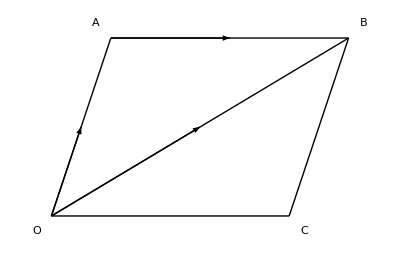

```mathematica
$DefaultFont = {"Courier", 14}
a1= Graphics[Arrow[{{0,0},{1,3}}]]; 
L1= Graphics[{Thick,Line[{{0,0},{2,6}}]}]; 
a2= Graphics[Arrow[{{2,6},{6,6}}]];
L2= Graphics[{Thick,Line[{{2,6},{10,6}}]}];
a3= Graphics[Arrow[{{0,0},{5,3}}]];
L3= Graphics[{Thick,Line[{{0,0},{10,6}}]}];
L4 =  Graphics[Line[{{0,0},{8,0}}]];
L5 =  Graphics[Line[{{8,0},{10,6}}]];
t1 = Graphics[Style[Text["O",{-0.5,-0.5}],18]];
t2 = Graphics[Style[Text["A",{-0.5+2,-0.5+7}],18]];
t3 = Graphics[Style[Text["B",{-0.5+11,-0.5+7}],18]];
t4= Graphics[Style[Text["C",{-0.5+9,-0.5}],18]];

Show[a1,L1,a2,L2,a3,L3,L4,L5,t1,t2,t3,t4]
```

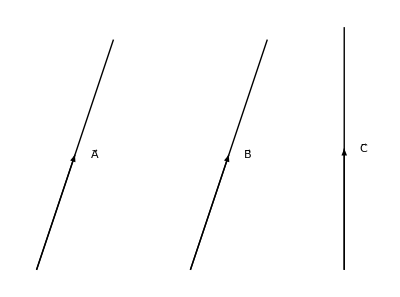

```mathematica
a1= Graphics[Arrow[{{0,0},{1,3}}]]; 
L1= Graphics[{Thick,Line[{{0,0},{2,6}}]}]; 
a5 = Graphics[Arrow[{{4,0},{5,3}}]]; 
L5 =  Graphics[{Thick,Line[{{4,0},{6,6}}]}];
a6 = Graphics[Arrow[{{8,0},{8,Sqrt[40]/2}}]]; 
L6 =  Graphics[{Thick,Line[{{8,0},{8,Sqrt[40]}}]}];
t5 = Graphics[Style[Text["C⃗",{8+0.5,Sqrt[40]/2}],18]];
t1 = Graphics[Style[Text["A⃗",{1+0.5,3}],18]];
(*t2 = Graphics[Style[Text["A",{-0.5+2,-0.5+7}],18]];*)
t3 = Graphics[Style[Text["B⃗",{5+0.5,3}],18]];
(*t4= Graphics[Style[Text["C",{-0.5+9-4,-0.5}],18]]; *)
Show[a1,L1,a5, L5,t1,t3,a6,L6,t5]
```

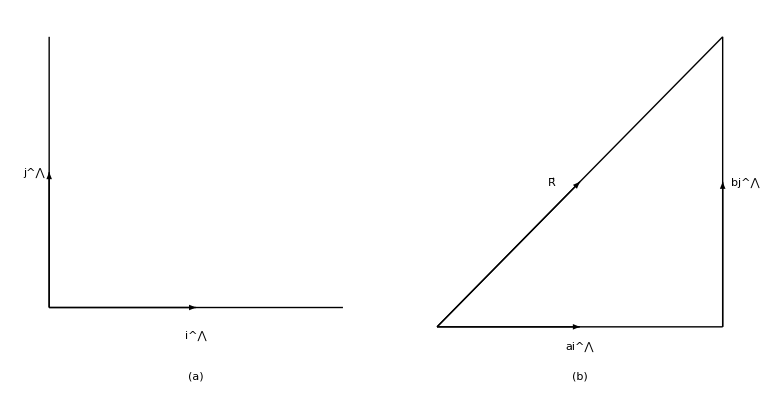

```mathematica
a1= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1,0}}]}]; 
L1= Graphics[{Thick,Line[{{0,0},{2,0}}]}]; 
a2= Graphics[{Arrowheads[Large],Arrow[{{0,0},{0,1}}]}]; 
L2= Graphics[{Thick,Line[{{0,0},{0,2}}]}]; 

a3= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1.25,0}}]}]; 
L3= Graphics[{Thick,Line[{{0,0},{2.5,0}}]}]; 
a4= Graphics[{Arrowheads[Large],Arrow[{{2.5,0},{2.5,1.5}}]}]; 
L4= Graphics[{Thick,Line[{{2.5,0},{2.5,3.0}}]}];
a5= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1.25,1.5}}]}]; 
L5= Graphics[{Thick,Line[{{0,0},{2.5,3.0}}]}];

t1 = Graphics[Style[Text["i^⋀",{1.0,-0.2}],18]];
t2 = Graphics[Style[Text["j^⋀",{-0.1,1}],18]];
t3 = Graphics[Style[Text["R⃗",{1,1.5}],18]];
t4= Graphics[Style[Text["ai^⋀",{1.25,-0.2}],18]];
t5= Graphics[Style[Text["bj^⋀",{2.7,1.5}],18]];

fa = Graphics[Style[Text["(a)",{1.0,-0.5}],18]];
fb= Graphics[Style[Text["(b)",{1.25,-0.5}],18]];

g1 =Show[a1,L1,a2,L2,t1,t2,fa];
g2 = Show[ a3,L3,a4,L4,a5,L5,t3,t4,t5,fb];
GraphicsRow[{g1,g2}]
```

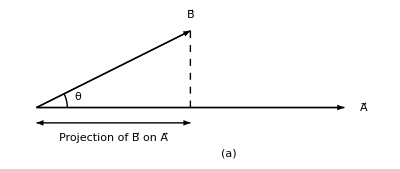

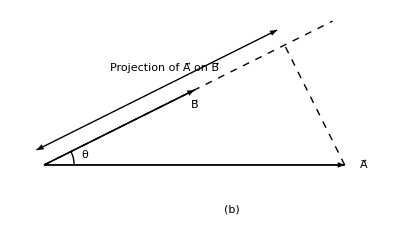

```mathematica
a1= Graphics[Arrow[{{0,0},{4,0}}]]; 
L1= Graphics[{Thick,Line[{{0,0},{4,0}}]}]; 
t1 = Graphics[Style[Text["A⃗",{4+0.25,0}],18]];

a2 = Graphics[Arrow[{{0,0},{2,1}}]]; 
L2 =  Graphics[{Thick,Line[{{0,0},{2,1}}]}];
t2 = Graphics[Style[Text["B⃗",{2,1+0.2}],18]];

L3 = Graphics[Circle[{0,0},0.4,{0,ArcTan[1/2]}]];
t3 = Graphics[Style[Text["θ",{0.6Cos[ArcTan[1/2]],0.3Sin[ArcTan[1/2]]}],18]];

L4 = Graphics[{Dashed, Thick,Line[{{2,0},{2,1}}]}];

a4 = Graphics[{Arrowheads[{-.05,.05}],Arrow[{{0,0-0.2},{2,0-0.2}}]}]; 
t4 = Graphics[Style[Text["Projection of B⃗ on A⃗",{1,0-0.4}],16]];
t1Label = Graphics[Style[Text["(a)",{2+0.5,0-0.6}],18]];


t2a = Graphics[Style[Text["B⃗",{2,1-0.2}],18]];L5 = Graphics[{Dashed, Thick,Line[{{0,0},{3.2*1.2,1.6*1.2}}]}];
L6 = Graphics[{Dashed, Thick,Line[{{4,0},{3.2,1.6}}]}];
t5 = Graphics[Style[Rotate[Text["Projection of A⃗ on B⃗",{1.6,1+0.3}],ArcTan[1/2]],16]];
a5 = Graphics[{Arrowheads[{-.05,.05}],Arrow[{{0-0.1,0+0.2},{3.2-0.1,1.6+0.2}}]}]; 
t2Label = Graphics[Style[Text["(b)",{2+0.5,0-0.6}],18]];


g1 = Show[a1,L1,t1,a2, L2,t2,L3,t3,a4,L4,t4, t1Label]
g2 = Show[a1,L1,t1,a2, L2,t2a,L3,t3,L5,L6,t5,a5, t2Label]
```

```mathematica
Solve[{y==0.5 x,y==-2x+8},{x,y}]
```

{{x→3.2,y→1.6}}

{Courier,14}

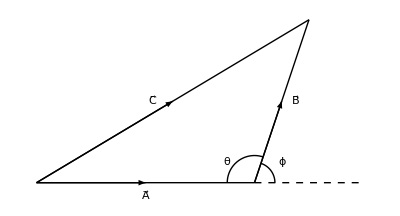

```mathematica
$DefaultFont = {"Courier", 14}

a1= Graphics[Arrow[{{0,0},{4,0}}]];
L1= Graphics[{Thick,Line[{{0,0},{8,0}}]}];
t1 = Graphics[Style[Text["A⃗",{4,-0.5}],18]];

a2= Graphics[Arrow[{{8,0},{9,3}}]]; 
L2= Graphics[{Thick,Line[{{8,0},{10,6}}]}]; 
t2 = Graphics[Style[Text["B⃗",{9+0.5,3}],18]];

a3= Graphics[Arrow[{{0,0},{5,3}}]];
L3= Graphics[{Thick,Line[{{0,0},{10,6}}]}];
t3= Graphics[Style[Text["C⃗",{5-0.75,3}],18]];

L4 =  Graphics[{Dashed,Thick,Line[{{8,0},{12,0}}]}];
arc1 = Graphics[Circle[{8,0},0.75,{0,ArcTan[3]}]];
t4 =  Graphics[Style[Text["ϕ",{9,0.75}],18]];
arc2 = Graphics[Circle[{8,0},1,{ArcTan[3],Pi}]];
t5 =  Graphics[Style[Text["θ",{7,0.75}],18]];

Show[a1,L1,t1,a2,L2,t2, a3,L3,t3, L4, arc1,t4, arc2, t5]
```

{Courier,14}

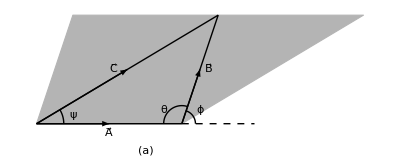

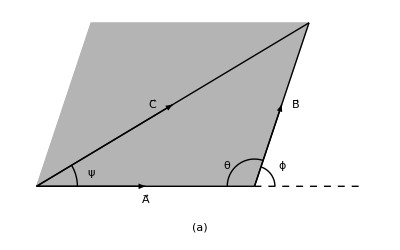

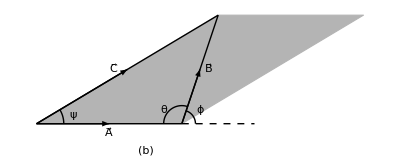

```mathematica
$DefaultFont = {"Courier", 14}

a1= Graphics[Arrow[{{0,0},{4,0}}]];
L1= Graphics[{Thick,Line[{{0,0},{8,0}}]}];
t1 = Graphics[Style[Text["A⃗",{4,-0.5}],18]];

a2= Graphics[Arrow[{{8,0},{9,3}}]]; 
L2= Graphics[{Thick,Line[{{8,0},{10,6}}]}]; 
t2 = Graphics[Style[Text["B⃗",{9+0.5,3}],18]];

a3= Graphics[Arrow[{{0,0},{5,3}}]];
L3= Graphics[{Thick,Line[{{0,0},{10,6}}]}];
t3= Graphics[Style[Text["C⃗",{5-0.75,3}],18]];

L4 =  Graphics[{Dashed,Thick,Line[{{8,0},{12,0}}]}];
arc1 = Graphics[Circle[{8,0},0.75,{0,ArcTan[3]}]];
t4 =  Graphics[Style[Text["ϕ",{9,0.75}],18]];
arc2 = Graphics[Circle[{8,0},1,{ArcTan[3],Pi}]];
t5 =  Graphics[Style[Text["θ",{7,0.75}],18]];

arc3 = Graphics[Circle[{0,0},1.5,{0,ArcTan[3/5]}]];
t6 =  Graphics[Style[Text["ψ",{2,0.5}],18]];

poly1 = Graphics[{EdgeForm[Dashed],Lighter[Lighter[Lighter[GrayLevel[0.001]]]],Polygon[{{0,0},{8,0},{10,6},{2,6}}]}];

poly2= Graphics[{EdgeForm[Dashed],Lighter[Lighter[Lighter[GrayLevel[0.001]]]],Polygon[{{0,0},{8,0},{10+8,6},{10,6}}]}];

f1Label = Graphics[Style[Text["(a)",{6,-1.5}],18]];
f2Label = Graphics[Style[Text["(b)",{6,-1.5}],18]];
g1 = Show[poly1,a1,L1,t1,a2,L2,t2, a3,L3,t3, L4, arc1,t4, arc2, t5,arc3,t6, f1Label]
g2 = Show[poly1,poly2,a1,L1,t1,a2,L2,t2, a3,L3,t3, L4, arc1,t4, arc2, t5,arc3,t6, f1Label]
g3= Show[poly2,a1,L1,t1,a2,L2,t2, a3,L3,t3, L4, arc1,t4, arc2, t5,arc3,t6,f2Label]
```

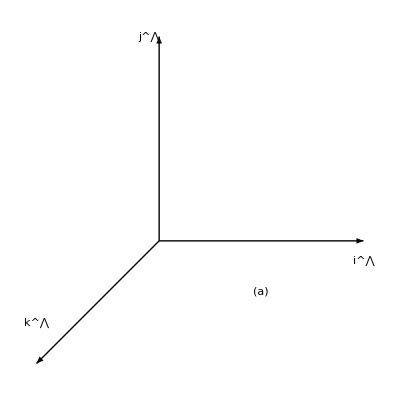

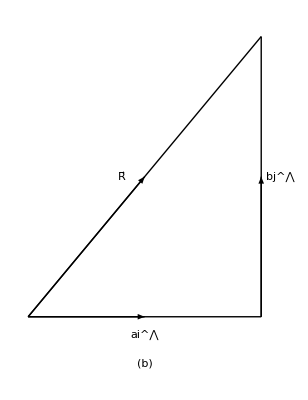

```mathematica
a1= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{2,0}}]}]; 

a2= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{0,2}}]}]; 


az= Graphics[{Arrowheads[Large],Thick, Arrow[{{0,0},{-1.2,-1.2}}]}]; 



a3= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1.25,0}}]}]; 
L3= Graphics[{Thick,Line[{{0,0},{2.5,0}}]}]; 
a4= Graphics[{Arrowheads[Large],Arrow[{{2.5,0},{2.5,1.5}}]}]; 
L4= Graphics[{Thick,Line[{{2.5,0},{2.5,3.0}}]}];
a5= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1.25,1.5}}]}]; 
L5= Graphics[{Thick,Line[{{0,0},{2.5,3.0}}]}];

t1 = Graphics[Style[Text["i^⋀",{2.0,-0.2}],18]];
t2 = Graphics[Style[Text["j^⋀",{-0.1,2}],18]];
tz = Graphics[Style[Text["k^⋀",{-1.2,-0.8}],18]];
t3 = Graphics[Style[Text["R⃗",{1,1.5}],18]];
t4= Graphics[Style[Text["ai^⋀",{1.25,-0.2}],18]];
t5= Graphics[Style[Text["bj^⋀",{2.7,1.5}],18]];

fa = Graphics[Style[Text["(a)",{1.0,-0.5}],18]];
fb= Graphics[Style[Text["(b)",{1.25,-0.5}],18]];

g1 =Show[a1,a2,az, t1,t2,tz, fa]
g2 = Show[ a3,L3,a4,L4,a5,L5,t3,t4,t5,fb]
(* GraphicsRow[{g1,g2}]*)
```

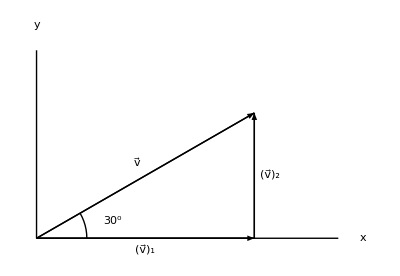

```mathematica
arc = Graphics[Circle[{0,0},0.2,{0,Pi/6}]];
tarc = Graphics[Style[Text["30^0",{0.25+.05,0.07}],18]];
L1= Graphics[{Thick,Line[{{0,0},{1.2,0}}]}]; 
L2= Graphics[{Thick,Line[{{0,0},{0,0.75}}]}]; 
t1 = Graphics[Style[Text["x",{1.2+0.1,0}],18]];
t2 = Graphics[Style[Text["y",{0,0.75+0.1}],18]];
a3= Graphics[{Arrowheads[Large],Arrow[{{0,0},{1Cos[Pi/6],0}}]}]; 
L3= Graphics[{Thick,Line[{{0,0},{Cos[Pi/6],0}}]}]; 
a4= Graphics[{Arrowheads[Large],Arrow[{{0,0},{Cos[Pi/6],1Sin[Pi/6]}}]}]; 
L4= Graphics[{Thick,Line[{{Cos[Pi/6],0},{Cos[Pi/6],Sin[Pi/6]}}]}];
a5= Graphics[{Arrowheads[Large],Arrow[{{Cos[Pi/6],0},{Cos[Pi/6],1Sin[Pi/6]}}]}]; 
L5= Graphics[{Thick,Line[{{0,0},{Cos[Pi/6],Sin[Pi/6]}}]}];

(* t3 = Graphics[Rotate[Style[Text["2 m/s",{0.3,0.5Sin[Pi/6]}],18],Pi/6]]; *)
t3 = Graphics[Rotate[Style[Text["v⃗",{0.4,0.6Sin[Pi/6]}],18],Pi/6]];
(* t4= Graphics[Style[Text["√3 m/s",{0.5Cos[Pi/6],-0.1}],18]]; *)
 t4= Graphics[Style[Text["(v⃗)_1",{0.5Cos[Pi/6],-0.05}],18]];
(* t5= Graphics[Style[Text["1 m/s",{1,0.5Sin[Pi/6]}],18]]; *)
t5= Graphics[Style[Text["(v⃗)_2",{0.93,0.5Sin[Pi/6]}],18]];

fa = Graphics[Style[Text["(a)",{1.0,-0.5}],18]];
fb= Graphics[Style[Text["(b)",{1.25,-0.5}],18]];


g2 = Show[L1,L2,t1,t2, a3,L3,a4,L4,a5,L5,t3,t4,t5,arc,tarc]
```

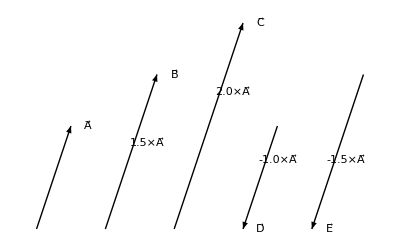

```mathematica
(* vec-base *)
theta = ArcTan[3];
a1= Graphics[Arrow[{{0,0},{1,3}}]]; 

a2 = Graphics[Arrow[{{2,0},{2+1.5,4.5}}]]; 
a3 = Graphics[Arrow[{{4,0},{4+2,6}}]]; 
a4 = Graphics[Arrow[{{6+1,+3},{6-1+1,-3+3}}]]; 
a5 = Graphics[Arrow[{{8+1.5,4.5},{8,0}}]]; 

t1 = Graphics[Style[Text["A⃗",{1+0.5,3}],18]];
t2 = Graphics[Style[Text["B⃗",{2+1.5+0.5,4.5}],18]];
t2a = Graphics[Rotate[Style[Text["1.5×A⃗",{2+1.5+0.5-.8,4.5-2}],18],theta]];
t3 = Graphics[Style[Text["C⃗",{4+2+0.5,6}],18]];
t3a = Graphics[Rotate[Style[Text["2.0×A⃗",{4+2+0.5-0.8,6-2}],18],theta]];
t4 = Graphics[Style[Text["D⃗",{6-1+1+0.5,-3+3}],18]];
t4a = Graphics[Rotate[Style[Text["-1.0×A⃗",{6-1+1+0.5+.5,-3+3+2}],18],theta]];
t5 = Graphics[Style[Text["E⃗",{8+.5,0}],18]];
t5a = Graphics[Rotate[Style[Text["-1.5×A⃗",{8+1,2}],18],theta]];

(*t2 = Graphics[Style[Text["A",{-0.5+2,-0.5+7}],18]];*)

(*t4= Graphics[Style[Text["C",{-0.5+9-4,-0.5}],18]]; *)
Show[a1,a2, a3, a4, t1,t2,t3,t4, t2a, t3a, t4a, a5,t5,t5a]
```

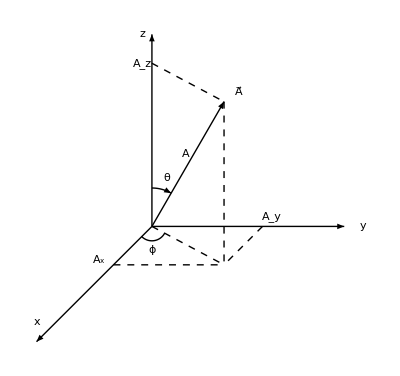

```mathematica
arcArrow[centre_,radius_,phi1_,phi2_,resolution_: 60]:=Arrow@Table[centre+radius {Cos[phi],Sin[phi]},{phi,phi1,phi2,(phi2-phi1)/Ceiling[(-phi2+phi1)/(Pi/resolution)]}];
arcArrowForward[centre_,radius_,phi1_,phi2_,resolution_: 60]:=Arrow@Table[centre+radius {Cos[phi],Sin[phi]},{phi,phi1,phi2,(phi2-phi1)/Ceiling[(phi2-phi1)/(Pi/resolution)]}];
(* 'resolution' is the number of segments to use for a 180 degree arc. *)
(* Usage: Graphics[arcArrow[{0,0},1,0.8,3.14]] *)
ay= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{2,0}}]}]; 

az= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{0,2}}]}]; 


ax= Graphics[{Arrowheads[Large],Thick, Arrow[{{0,0},{-1.2,-1.2}}]}]; 

av= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},1.5{Cos[Pi/3],Sin[Pi/3]}}]}]; 

L1= Graphics[{Dashed,Thick,Line[{1.5{Cos[Pi/3],Sin[Pi/3]},{1.5 Cos[Pi/3],-0.4}}]}]; 
L2= Graphics[{Dashed,Thick,Line[{{0,0},{1.5 Cos[Pi/3],-0.4}}]}]; 
L3= Graphics[{Dashed,Thick,Line[{{0,1.5Sin[Pi/3]+0.4},{1.5 Cos[Pi/3],1.5Sin[Pi/3]}}]}]; 

Lx= Graphics[{Dashed,Thick, Line[{{1.15,0},{1.15-0.4,-0.4}}]}]; 
Ly= Graphics[{Dashed,Thick, Line[{{-0.4,-0.4},{-0.4+1.15,-0.4}}]}]; 


ty = Graphics[Style[Text["y",{2.2,0}],18]];
tz = Graphics[Style[Text["z",{-0.1,2}],18]];
tx = Graphics[Style[Text["x",{-1.2,-1}],18]];
ta = Graphics[Style[Text["A⃗",{1,1.5}],18]];
tax= Graphics[Style[Text["A_x",{1.25,-0.2}],18]];
tay= Graphics[Style[Text["A_y",{2.7,1.5}],18]];
taz= Graphics[Style[Text["A_y",{2.7,1.5}],18]];
arct = Graphics[{Thick,arcArrow[{0,0},0.4,Pi/2,Pi/3]}];
arcp = Graphics[{Thick,Circle[{0,0},0.15,{ArcTan[(-0.4)/(1.5 Cos[Pi/3])]+Pi+Pi/2-Pi/10,ArcTan[-1.2/-1.2]+Pi+Pi/2+Pi/10}]}];

tarct = Graphics[Style[Text["θ",{0.15,0.5}],18]];
tarcp = Graphics[Style[Text["ϕ",{0,-0.25}],18]];

vx = Graphics[Style[Text["A_x",{-0.55,-0.35}],18]];
vy = Graphics[Style[Text["A_y",{1.25,0.1}],18]];
vz = Graphics[Style[Text["A_z",{-0.1,1.7}],18]];
vec = Graphics[Style[Text["A⃗",{0.9,1.4}],18]];
v = Graphics[Style[Text["A",{0.35,0.75}],18]];

fa = Graphics[Style[Text["(a)",{1.0,-0.5}],18]];
fb= Graphics[Style[Text["(b)",{1.25,-0.5}],18]];



g1 =Show[ax,ay,az,av, tx,ty,tz,L1,L2,L3,arct,arcp,Lx,Ly,tarct,tarcp, vx,vy,vz,vec,v]
(* g2 = Show[ a3,L3,a4,L4,a5,L5,t3,t4,t5,fb] *)
```

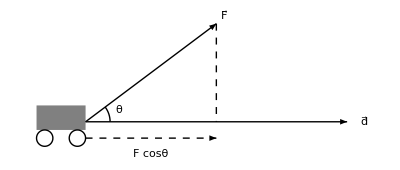

```mathematica
a1= Graphics[{Thick,Arrow[{{0,0},{4,3}}]}];
(* L1= Graphics[{Thick,Line[{{0,0},{8,0}}]}]; *)
t1 = Graphics[Style[Text["F⃗",{4.25,3.25}],18]];

a2= Graphics[{Thick,Arrow[{{0,0},{8,0}}]}]; 
(* L2= Graphics[{Thick,Line[{{8,0},{10,6}}]}]; *) 
t2 = Graphics[Style[Text["d⃗",{8+0.5,0}],18]];

L1= Graphics[{Thick,Dashed,Line[{{4,3},{4,0}}]}];

(*a3= Graphics[Arrow[{{0,0},{5,3}}]];
L3= Graphics[{Thick,Line[{{0,0},{10,6}}]}];
t3= Graphics[Style[Text["C⃗",{5-0.75,3}],18]]; *)

(* L4 =  Graphics[{Dashed,Thick,Line[{{8,0},{12,0}}]}]; *)
arc1 = Graphics[Circle[{0,0},0.75,{0,ArcTan[3/4]}]];
t4 =  Graphics[Style[Text["θ",{1,0.35}],18]];

rect = Graphics[{Gray,Rectangle[{-1.5,-0.25},{0,0.5}]}];
a3= Graphics[{Dashed,Thick,Arrow[{{0,-0.5},{4,-0.5}}]}];
t3 = Graphics[Style[Text["F cosθ",{2,-1}],18]]; 

wheel1 = Graphics[Circle[{-0.25,-0.5},0.25,{0,2Pi}]];
wheel2 = Graphics[Circle[{-1.25,-0.5},0.25,{0,2Pi}]];
(* arc2 = Graphics[Circle[{8,0},1,{ArcTan[3],Pi}]];
t5 =  Graphics[Style[Text["θ",{7,0.75}],18]]; *)

Show[a1,t1,a2,t2, arc1,t4, L1,rect,a3,t3,wheel1,wheel2]
```

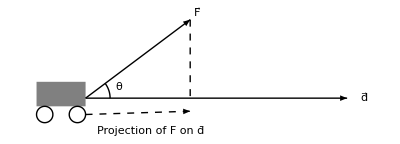

```mathematica
a1= Graphics[{Thick,Arrow[{{0,0},0.8{4,3}}]}];
(* L1= Graphics[{Thick,Line[{{0,0},{8,0}}]}]; *)
t1 = Graphics[Style[Text["F⃗",0.8{4.25,3.25}],18]];

a2= Graphics[{Thick,Arrow[{{0,0},{8,0}}]}]; 
(* L2= Graphics[{Thick,Line[{{8,0},{10,6}}]}]; *) 
t2 = Graphics[Style[Text["d⃗",{8+0.5,0}],18]];

L1= Graphics[{Thick,Dashed,Line[{0.8{4,3},0.8{4,0}}]}];

(*a3= Graphics[Arrow[{{0,0},{5,3}}]];
L3= Graphics[{Thick,Line[{{0,0},{10,6}}]}];
t3= Graphics[Style[Text["C⃗",{5-0.75,3}],18]]; *)

(* L4 =  Graphics[{Dashed,Thick,Line[{{8,0},{12,0}}]}]; *)
arc1 = Graphics[Circle[{0,0},0.75,{0,ArcTan[3/4]}]];
t4 =  Graphics[Style[Text["θ",{1,0.35}],18]];

rect = Graphics[{Gray,Rectangle[{-1.5,-0.25},{0,0.5}]}];
a3= Graphics[{Dashed,Thick,Arrow[{{0,-0.5},0.8{4,-0.5}}]}];
t3 = Graphics[Style[Text["Projection of F̄ on d̄",{2,-1}],18]]; 

wheel1 = Graphics[Circle[{-0.25,-0.5},0.25,{0,2Pi}]];
wheel2 = Graphics[Circle[{-1.25,-0.5},0.25,{0,2Pi}]];
(* arc2 = Graphics[Circle[{8,0},1,{ArcTan[3],Pi}]];
t5 =  Graphics[Style[Text["θ",{7,0.75}],18]]; *)

Show[a1,t1,a2,t2, arc1,t4, L1,rect,a3,t3,wheel1,wheel2]
```

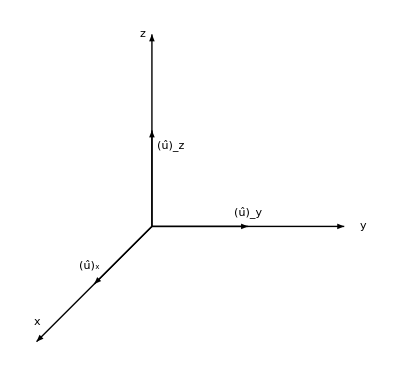

```mathematica
ay= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{2,0}}]}]; 
az= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{0,2}}]}]; 
ax= Graphics[{Arrowheads[Large],Thick, Arrow[{{0,0},{-1.2,-1.2}}]}]; 

uy= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{1,0}}]}]; 
uz= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{0,1}}]}]; 
ux= Graphics[{Arrowheads[Large],Thick, Arrow[{{0,0},0.5{-1.2,-1.2}}]}]; 


ty = Graphics[Style[Text["y",{2.2,0}],18]];
tz = Graphics[Style[Text["z",{-0.1,2}],18]];
tx = Graphics[Style[Text["x",{-1.2,-1}],18]];


tuy = Graphics[Style[Text["(û)_y",0.5{2.0,0.3}],18]];
tuz = Graphics[Style[Text["(û)_z",0.5{0.4,1.7}],18]];
tux = Graphics[Style[Text["(û)_x",0.5{-1.3,-0.8}],18]];

Show[ax,ay,az, ux,uy,uz,tx,ty,tz,tux,tuy,tuz]
```

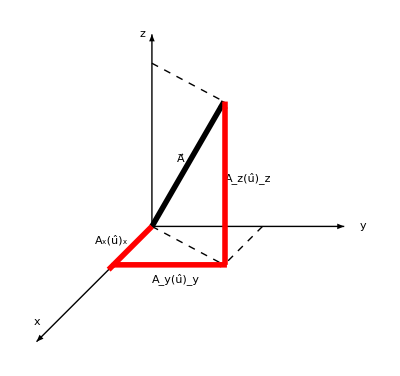

```mathematica
arcArrow[centre_,radius_,phi1_,phi2_,resolution_: 60]:=Arrow@Table[centre+radius {Cos[phi],Sin[phi]},{phi,phi1,phi2,(phi2-phi1)/Ceiling[(-phi2+phi1)/(Pi/resolution)]}];
arcArrowForward[centre_,radius_,phi1_,phi2_,resolution_: 60]:=Arrow@Table[centre+radius {Cos[phi],Sin[phi]},{phi,phi1,phi2,(phi2-phi1)/Ceiling[(phi2-phi1)/(Pi/resolution)]}];
(* 'resolution' is the number of segments to use for a 180 degree arc. *)
(* Usage: Graphics[arcArrow[{0,0},1,0.8,3.14]] *)



L1= Graphics[{Dashed,Thick,Line[{1.5{Cos[Pi/3],Sin[Pi/3]},{1.5 Cos[Pi/3],-0.4}}]}]; 
L2= Graphics[{Dashed,Thick,Line[{{0,0},{1.5 Cos[Pi/3],-0.4}}]}]; 
L3= Graphics[{Dashed,Thick,Line[{{0,1.5Sin[Pi/3]+0.4},{1.5 Cos[Pi/3],1.5Sin[Pi/3]}}]}]; 

Lx= Graphics[{Dashed,Thick, Line[{{1.15,0},{1.15-0.4,-0.4}}]}]; 
Ly= Graphics[{Dashed,Thick, Line[{{-0.4,-0.4},{-0.4+1.15,-0.4}}]}]; 


ty = Graphics[Style[Text["y",{2.2,0}],18]];
tz = Graphics[Style[Text["z",{-0.1,2}],18]];
tx = Graphics[Style[Text["x",{-1.2,-1}],18]];
ta = Graphics[Style[Text["A⃗",{1,1.5}],18]];
tax= Graphics[Style[Text["A_x",{1.25,-0.2}],18]];
tay= Graphics[Style[Text["A_y",{2.7,1.5}],18]];
taz= Graphics[Style[Text["A_y",{2.7,1.5}],18]];
arct = Graphics[{Thick,arcArrow[{0,0},0.4,Pi/2,Pi/3]}];
arcp = Graphics[{Thick,Circle[{0,0},0.15,{ArcTan[(-0.4)/(1.5 Cos[Pi/3])]+Pi+Pi/2-Pi/10,ArcTan[-1.2/-1.2]+Pi+Pi/2+Pi/10}]}];

tarct = Graphics[Style[Text["θ",{0.15,0.5}],18]];
tarcp = Graphics[Style[Text["ϕ",{0,-0.25}],18]];

vx = Graphics[Style[Text["A_x(û)_x",0.4{-0.65-0.4,-0.35}],18]];
vy = Graphics[Style[Text["A_y(û)_y",{1.25-0.4-0.6,0.15-0.4-0.3}],18]];
vz = Graphics[Style[Text["A_z(û)_z",{-0.2+1.2,1.7-0.6-0.6}],18]];
vec = Graphics[Style[Text["A⃗",{0.3,0.7}],18]];
v = Graphics[Style[Text["A",{0.35,0.75}],18]];

fa = Graphics[Style[Text["(a)",{1.0,-0.5}],18]];
fb= Graphics[Style[Text["(b)",{1.25,-0.5}],18]];

az= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{0,2}}]}]; 
ax= Graphics[{Arrowheads[Large],Thick, Arrow[{{0,0},{-1.2,-1.2}}]}];
ay= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,0},{2,0}}]}]; 


 av= Graphics[{Arrowheads[Large],Thickness[0.01],Arrow[{{0,0},1.5{Cos[Pi/3],Sin[Pi/3]}}]}]; 

aay= Graphics[{Arrowheads[Large],Thickness[0.01],Red,Arrow[{{0-0.4,0-0.4},{1.18-0.4,0-0.4}}]}]; 
aaz= Graphics[{Arrowheads[Large],Thickness[0.01],Red,Arrow[{{0-0.4+1.16,0-0.4},{0-0.4+1.16,1.7-0.4}}]}]; 
aax= Graphics[{Arrowheads[Large],Thickness[0.01],Red, Arrow[{{0,0},{-0.45,-0.45}}]}]; 




g1 =Show[ax,ay,az,av, tx,ty,tz,L1,L2,L3,Lx,Ly, vx,vy,vz,vec,aax,aay,aaz]
```

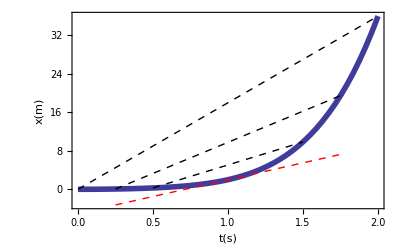

```mathematica
x[t_] = t^2+t^5;
dxdt[t_] = 2t+5t^4; m = dxdt[1];
y[t_] = m t -5;
a1= Graphics[{Thick,Dashed,Line[{{0,x[0]},{2,x[2]}}]}]; 
a2= Graphics[{Thick,Dashed,Line[{{.25,x[.25]},{1.75,x[1.75]}}]}]; 
a3= Graphics[{Thick,Dashed,Line[{{.5,x[.5]},{1.5,x[1.5]}}]}]; 
a4= Graphics[{Thick,Red,Dashed,Line[{{.25,y[.25]},{1.75,y[1.75]}}]}]; 
g=Plot[x[t],{t,0,2},PlotStyle->Thickness[0.01],PlotRange->All,TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14},
Frame->True, FrameLabel->{"t(s)", "x(m)"}, Axes->False];
Show[g,a1,a2,a3,a4]
```

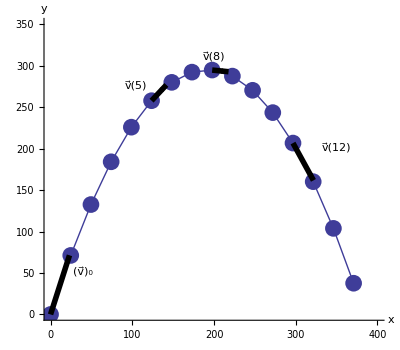

```mathematica
v0=80; dt = 1; npts = 16;g = 9.81;
theta=72; (* degrees *)
v0x = v0*Cos[theta*Pi/180.0];
v0y = v0*Sin[theta*Pi/180.0];
t = Table[(i-1)*dt, {i,1,npts}];
yData =Table[{v0y * t[[i]] -0.5*g*t[[i]]^2,v0y-g*t[[i]]},{i,1,npts}]; 
xyData = Table[{v0x * t[[i]],v0y * t[[i]] -0.5*g*t[[i]]^2},{i,1,npts}];
p1= ListPlot[xyData, PlotStyle->PointSize[0.03], AspectRatio->Automatic,TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14},
AxesLabel->{"x","y"},PlotRange->{{0,400},{0,350}}];
p2 = ListPlot[xyData, Joined->True];

 av= Graphics[{Arrowheads[Large],Thickness[0.01],Arrow[{{0,0},75{Cos[theta*Pi/180.0],Sin[theta*Pi/180.0]}}]}]; 

av1= Graphics[{Arrowheads[Large],Thickness[0.01],Arrow[{{v0x * t[[6]],v0y * t[[6]] -0.5*g*t[[6]]^2},{v0x * t[[6]],v0y * t[[6]] -0.5*g*t[[6]]^2}+20{Cos[0.35theta*Pi/180.0],Sin[theta*Pi/180.0]}}]}];

av2= Graphics[{Arrowheads[Large],Thickness[0.01],Arrow[{{v0x * t[[9]],v0y * t[[9]] -0.5*g*t[[9]]^2},{v0x * t[[9]],v0y * t[[9]] -0.5*g*t[[9]]^2}+20{1,-0.1}}]}];

av3= Graphics[{Arrowheads[Large],Thickness[0.01],Arrow[{{v0x * t[[13]],v0y * t[[13]] -0.5*g*t[[13]]^2},{v0x * t[[13]],v0y * t[[13]] -0.5*g*t[[13]]^2}+25{1,-1.8}}]}];
(* Print[v0x," {  ", v0y t[[4]]-0.5g*t[[4]]^2," ,  ", v0y-g*t[[4]], " },{  ", v0y t[[5]]-0.5g*t[[5]]^2," ,  ",v0y-g*t[[5]], " },{  ",v0y t[[6]]-0.5g*t[[6]]^2," ,  ", v0y-g*t[[6]]," } { ",v0y t[[7]]-0.5g*t[[7]]^2," ,  ", v0y-g*t[[7]]," },{  ",v0y t[[8]]-0.5g*t[[8]]^2," ,  ", v0y-g*t[[8]]," },{  ",v0y t[[9]]-0.5g*t[[9]]^2," ,  ", v0y-g*t[[9]]," },{  ",v0y t[[10]]-0.5g*t[[10]]^2," ,  ", v0y-g*t[[10]],"}"]
*)

ta = Graphics[Style[Text["(v⃗)_0",{40,50}],18]];
tb = Graphics[Style[Text["v⃗(5)",{105,275}],18]];
tc = Graphics[Style[Text["v⃗(8)",{200,310}],18]];
td = Graphics[Style[Text["v⃗(12)",{350,200}],18]];


Show[p1,p2,av,ta,tb,tc,td,av1,av2,av3]
```

```mathematica
yData
```

{{0.,76.0845},{71.1795,66.2745},{132.549,56.4645},{184.109,46.6545},{225.858,36.8445},{257.798,27.0345},{279.927,17.2245},{292.247,7.41452},{294.756,-2.39548},{287.456,-12.2055},{270.345,-22.0155},{243.425,-31.8255},{206.694,-41.6355},{160.154,-51.4455},{103.803,-61.2555},{37.6428,-71.0655}}

```mathematica
yData2= Table[{(yData[[i,1]]-184.109)/20,yData[[i,2]]},{i,1,Length[yData]}]
```

{{-9.20545,76.0845},{-5.64647,66.2745},{-2.578,56.4645},{-0.0000218045,46.6545},{2.08745,36.8445},{3.68443,27.0345},{4.79091,17.2245},{5.40688,7.41452},{5.53236,-2.39548},{5.16733,-12.2055},{4.31181,-22.0155},{2.96579,-31.8255},{1.12926,-41.6355},{-1.19776,-51.4455},{-4.01529,-61.2555},{-7.32331,-71.0655}}

```mathematica
Sqrt[2*9.8*2]
```

6.26099

```mathematica
%/Sqrt[2]
```

4.42719

```mathematica
6^2/(2*9.8)
```

1.83673

```mathematica
6.0/Sqrt[2]
```

4.24264

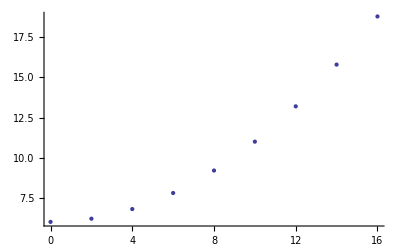

```mathematica
dat= {{0,6.0},
{2,6.2},
{4,6.8},
{6,7.8},
{8,9.2},
{10,11.0},
{12,13.2},
{14,15.8},
{16,18.8}
};
ListPlot[dat]
```

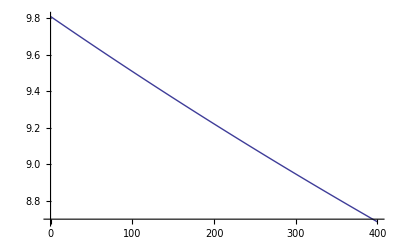

```mathematica
g[r_] = 9.81*6370^2/(6370+r)^2;
Plot[g[r],{r,0,400}]
```

```mathematica
x = Table[(i-1)*50,{i,1,11}];
y = Table[N[g[x[[i]]]],{i,1,11}];
z = MatrixForm[Table[{x[[i]],N[y[[i]],3], N[100*(9.81-y[[i]])/9.81]},{i,1,11}]]
```

(0 | 9.81 | 0.
50 | 9.65779 | 1.55157
100 | 9.5091 | 3.0673
150 | 9.36381 | 4.5483
200 | 9.22183 | 5.99561
250 | 9.08305 | 7.41026
300 | 8.94739 | 8.7932
350 | 8.81474 | 10.1454
400 | 8.68501 | 11.4677
450 | 8.55813 | 12.7611
500 | 8.43402 | 14.0263)

```mathematica
N[Sqrt[2],2]
```

1.4

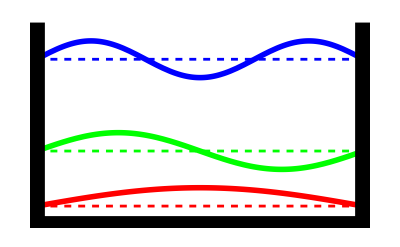

```mathematica
p1 = Plot[{1+Sin[Pi x],1,4+Sin[2Pi x],4, 9+Sin[3Pi x],9},{x,0,1}, PlotRange->{All,{0,11}}, PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False];
box =Graphics[{Thickness->0.03, Line[{{0,11},{0,0},{1,0},{1,11}}]}];
Show[p1,box]
```

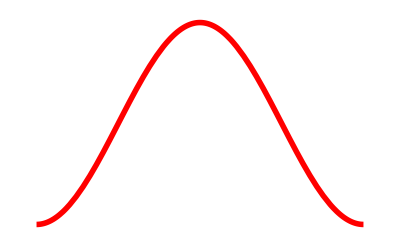

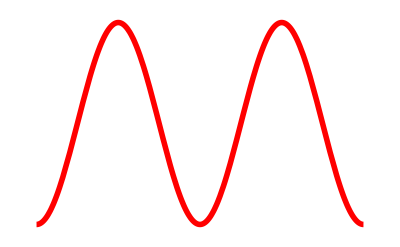

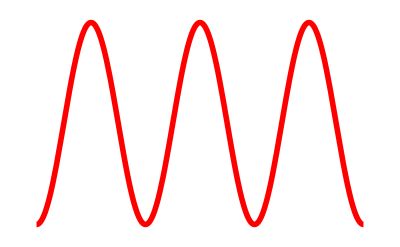

```mathematica
p1 = Plot[{ (Sin[Pi x])^2},{x,0,1}, PlotRange->All, PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False];

p2 = Plot[{  (Sin[2Pi x])^2},{x,0,1}, PlotRange->All, PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False];

p3 = Plot[{ (Sin[3Pi x])^2},{x,0,1}, PlotRange->All, PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False];


box =Graphics[{Thickness->0.03, Line[{{0,11},{0,0},{1,0},{1,11}}]}];
p1
p2
p3
```

```mathematica
\dfrac{6.63\times 10^{-34}\textrm{J.s}}{8\times 9.11\times 10^{-31}\times 2\times 52.9\times 10^{-12}\textrm{m}}
```

```mathematica
(6.63*10^(-34))^2/(8*9.11*10^(-31)*(2*52.9*10^(-12))^2)
```

5.38825×10^-18

```mathematica
%*4
```

2.1553×10^-17

```mathematica
%*9/4
```

4.84942×10^-17

```mathematica
3*10^8/((21.553 - 5.388)*10^(-18)/(6.63*10^(-34)))
```

```mathematica
1.2304361274358183*^-8
Sin[4*Pi/3.0]
```

1.23044×10^-8

-0.866025

```mathematica
(1.0/3)*(1 - 9.0/(8*Pi))
```

0.213967

```mathematica
Sin[4*Pi/3.0]
```

-0.866025

```mathematica
\dfrac{1}{3}+ \dfrac{\sqrt{3}}{4\pi}
```

```mathematica
1/3.0 + Sqrt[3.0]/(4 Pi)
```

0.471166

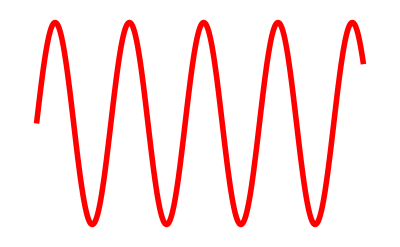

```mathematica
p = Plot[{ (Sin[8.8Pi x])},{x,0,1}, PlotRange->All, PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False]
```

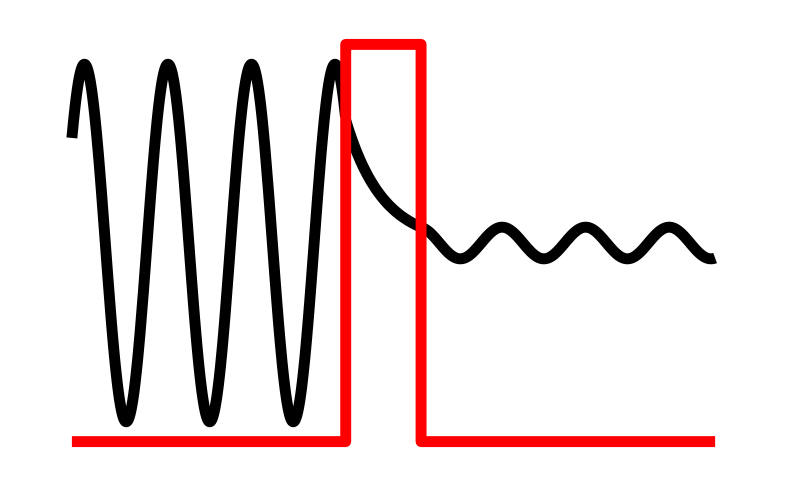

```mathematica
f[x_] = Piecewise[{ {0.9Sin[8.8Pi x], x<0.995},{Exp[-((x-1)/0.1)]Sin[8.8Pi ], 0.995<=x<1.2}, {Sin[8.8Pi ]Exp[-((1.2-1)/0.1)]Sin[8.8Pi (x)], x>1.2} }];
p = Plot[f[x],{x,0.25,2.0},PlotRange->All, PlotStyle->{{Thickness->0.01, Black}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}, Axes->False];
extra = -1;
pot=Graphics[{Thickness->0.01, Red,Line[{{0.25,0+extra},{0.995,0+extra},{0.995,2+extra},{1.2,2+extra}, {1.2,0+extra}, {2, 0+extra}}]}];
Show[p,pot]
```

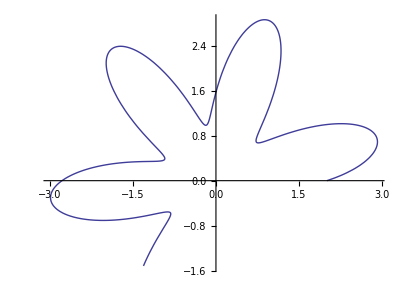

```mathematica
PolarPlot[2+Sin[2 Pi t],{t,0,4}]
```

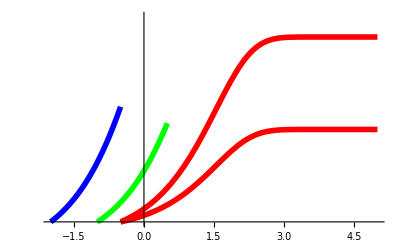

```mathematica
p1 = Plot[{Tanh[Exp[v+0.5]/10]-0.1,2*(Tanh[Exp[v+0.5]/10]-0.1)},{v,-2,5}, PlotRange->{{-2,5},{0,2}},PlotStyle->{{Thickness->0.01, Red}},Ticks->{True, False},TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}] ;
p2 = Plot[{3.0*(Tanh[Exp[v+1]/10]-0.1)},{v,-2,0.5}, PlotRange->{{-2,1},{0,2}},PlotStyle->{{Thickness->0.01, Green}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}];
p3 = Plot[{3.5*(Tanh[Exp[v+2.0]/10]-0.1)},{v,-2,-0.5}, PlotRange->{{-2,1},{0,2}},PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}];
Labeled[Show[p1,p2,p3],""]
```

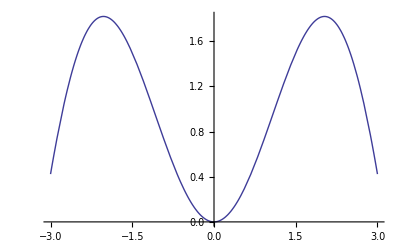
-Graphics-E/T

```mathematica
Labeled[Plot[Sin[x] x,{x,-3,3}],"E/T"]
```

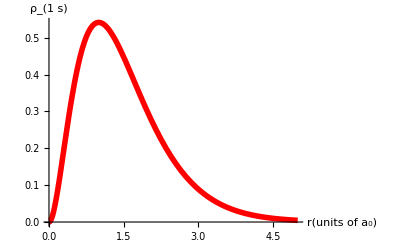

```mathematica
Plot[4r^2Exp[-2r],{r, 0, 5},AxesLabel->{"r(units of a_0)", "ρ_(1  s)"},
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->14}]
```

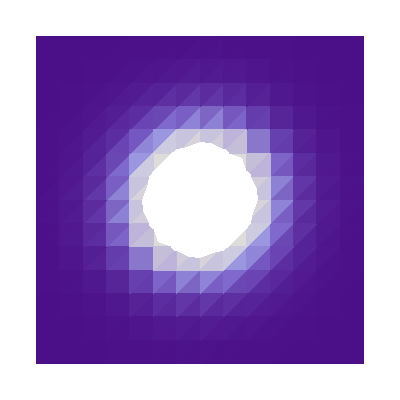

```mathematica
DensityPlot[(1/Pi)Exp[-2Sqrt[x^2+y^2]],{x,-4,4},{y,-4,4}, Axes->False, Frame->False]
```

```mathematica
10.2/4.14
```

2.46377

```mathematica
1.9/0.414
```

4.58937

```mathematica
(6.63*10^(-34)/(2Pi))*2
```

2.11039×10^-34

```mathematica
(180.0/Pi)*ArcCos[1/Sqrt[6]]
```

65.9052

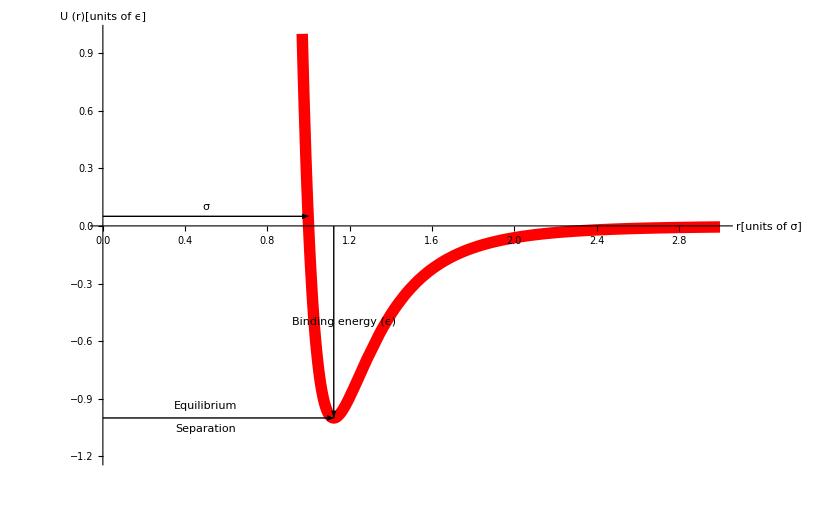

```mathematica
p=Plot[4*((1/r)^12 - (1/r)^6),{r, 0.1, 3},AxesLabel->{"r[units of σ]", "U (r)[units of ϵ]"},PlotRange->{{0,3},{-1.2,1}},
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->18}];
a1 = Graphics[{Arrowheads[Large],Thick,Arrow[{{2^(1/6),0},{2^(1/6),-1.0}}]}];
t1 = Graphics[Style[Rotate[Text["Binding energy (ϵ)",{2^(1/6)+0.05,-0.5}],90 Degree],22]];
a2= Graphics[{Arrowheads[Medium],Thick,Arrow[{{0,0.05},{1,0.05}}]}];
t2 = Graphics[Style[Text["σ",{0.5,0.1}],22]];
a3= Graphics[{Arrowheads[Large],Thick,Arrow[{{0,-1},{2^(1/6),-1}}]}];
t3 = Graphics[Style[Text["Equilibrium",{0.5,-0.94}],22]];
t4 = Graphics[Style[Text["Separation",{0.5,-1.06}],22]];
Show[p,a1,t1,a2,t2,a3,t3,t4]
```

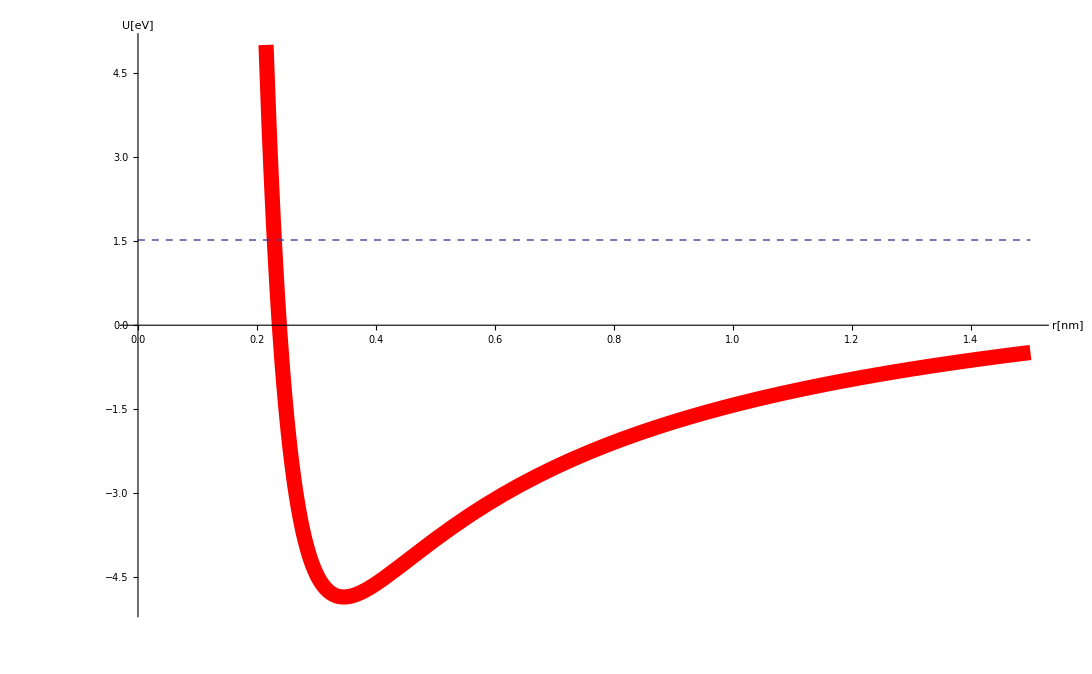

```mathematica
p1= Plot[1.6+4.2*4*(40(0.2/(r+0.11))^8 - (0.2/(r+0.11))^1.0),{r, 0.1, 1.5},AxesLabel->{"r[nm]", "U[eV]"},PlotRange->{{0,1.5},{-5,5}},
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
L1 = Plot[1.52,{r, 0, 1.5}, PlotStyle->{Dashed}];
Show[p1,L1]
```

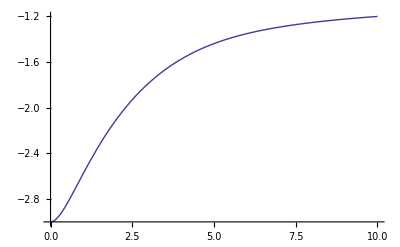

```mathematica
s[r_] = (1 + r + r^2/3) Exp[-r];
en[r_]=-1- (2/(1+s[r])) *(1/r- (1/r) * (1+r) Exp[-2r]+(1+r) Exp[-r]);
Plot[en[r], {r,0,10}]
```

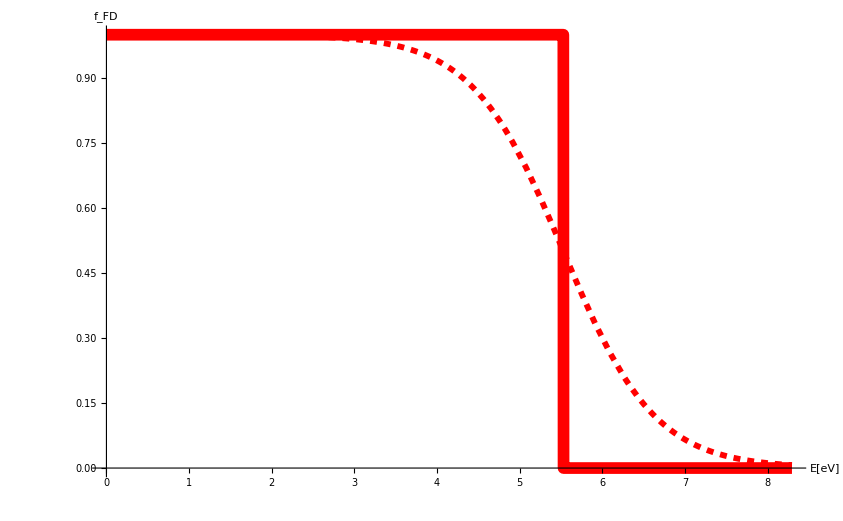

```mathematica
kb = 0.00008629055; (* in units of eV/K *)
ef = 5.53; (* Fermi of gold in eV *)
f[e_,t_] = 1/(Exp[(e-ef)/(kb *t)]+1); (* Fermi-Dirac *)
p1 = Plot[{f[e,0.0001],f[e,0.1*64200]},{e,0,1.5*ef},AxesLabel->{"E[eV]", "f_FD"}, 
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.005,Red},{Thickness->0.01, Green},{Dashed,Thickness->0.005,Green},{Thickness->0.01,Blue},{Dashed,Thickness->0.005,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
Show[p1]
```

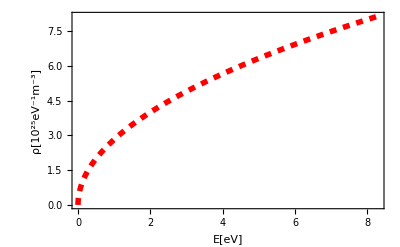

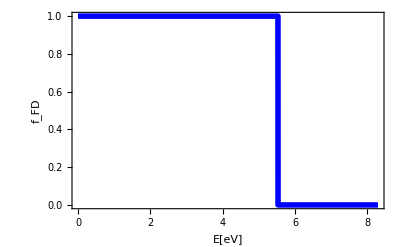

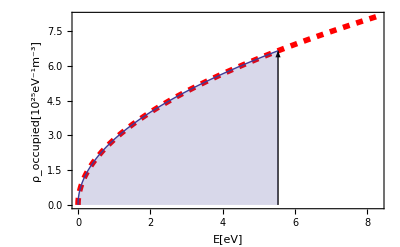

```mathematica
kb = 0.00008629055; (* in units of eV/K *)
ef = 5.53; (* Fermi of gold in eV *)
f[e_,t_] = 1/(Exp[(e-ef)/(kb *t)]+1); (* Fermi-Dirac *)
p1 = Plot[{f[e,0.0001]},{e,0,1.5*ef}, Frame->True,FrameLabel->{"E[eV]", "f_FD"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
 mc2 = 0.521*10^6; (* electron rest*)
hbartimesc = 1.23984193 *10^(-6);(*eV.meter *)
xx= Pi *Sqrt[2] *(mc2/(Pi^2 * hbartimesc^2))^(3/2);
rho[e_] = xx * Sqrt[e]/10^(25);
p2  = Plot[rho[e], {e, 0, 1.5*ef},Frame->True,FrameLabel->{"E[eV]", "ρ[10^25eV^-1m^-3]"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Red,Dashed}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
p2a  = Plot[rho[e], {e, 0, 1.5*ef},Frame->True,FrameLabel->{"E[eV]", "ρ_occupied[10^25eV^-1m^-3]"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Red,Dashed}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
p3 = Plot[rho[e], {e, 0, ef}, Filling->Axis];
line =  Graphics[Line[{{ef,0},{ef,rho[ef]}}]]; 
Show[p2]
Show[p1]
Show[p2a,p3,line]
```

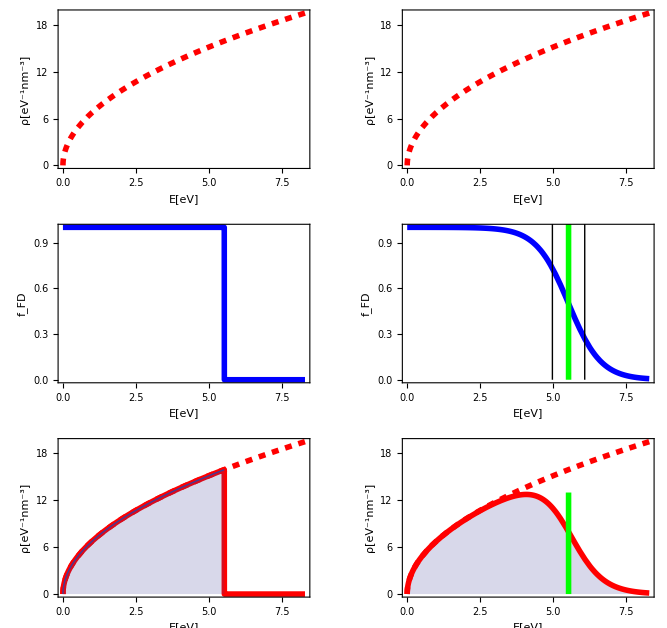

```mathematica
ef = 5.53*1.6*10^(-19); (* J *) 
hbar = 6.63*10^(-34)/(2*Pi); (* J.s*) kb = 0.00008629055*1.6*10^(-19); (* in units of J/K *)
me = 9.1*10^(-31); (* kg *)
den[en_] = Pi * Sqrt[2]* ( me/(Pi^2*hbar^2))^(3/2)*Sqrt[en] *1.6*10^(-19)*10^(-27); (* per eV per nm^3 *) (* en in J *)
f[en_,t_] = 1/(Exp[(en-ef)/(kb *t)]+1); (* Fermi-Dirac *)

p2  = Plot[den[e*1.6*10^(-19)], {e, 0, 1.5*ef/(1.6*10^(-19))},Frame->True,FrameLabel->{"E[eV]", "ρ[eV^-1nm^-3]"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Red,Dashed}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
 p1 = Plot[{f[e*1.6*10^(-19),0.0001]},{e,0,1.5*ef/(1.6*10^(-19))}, Frame->True,FrameLabel->{"E[eV]", "f_FD"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
p2a  = Plot[den[e*1.6*10^(-19)]*f[e*1.6*10^(-19),0.0001], {e, 0, 1.5*ef/(1.6*10^(-19))},Frame->True,FrameLabel->{"E[eV]", "ρ_occupied[eV^-1nm^-3]"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Red}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
p3 = Plot[den[e*1.6*10^(-19)], {e, 0, ef/(1.6*10^(-19))}, Filling->Axis];
 p3a = Show[p2,p2a,p3];

temp = 0.1*64200;
 p1a = Plot[{f[e*1.6*10^(-19),temp]},{e,0,1.5*ef/(1.6*10^(-19))}, Frame->True,FrameLabel->{"E[eV]", "f_FD"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
p3aa = Plot[den[e*1.6*10^(-19)]*f[e*1.6*10^(-19),temp], {e, 0, 1.5*ef/(1.6*10^(-19))}, Filling->Axis,Frame->True,FrameLabel->{"E[eV]", "ρ_occupied[eV^-1nm^-3]"}, RotateLabel->True,
 PlotStyle->{{Thickness->0.01, Red}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
line = Graphics[ {Green,Thickness[0.01], Line[ { {ef/(1.6*10^(-19)),0}, {ef/(1.6*10^(-19)),13}}]}];
line1 = Graphics[ Line[ { {ef/(1.6*10^(-19))-kb*temp/(1.6*10^(-19)),0}, {ef/(1.6*10^(-19))-kb*temp/(1.6*10^(-19)),13}}]];
line2 = Graphics[ Line[ { {ef/(1.6*10^(-19))+kb*temp/(1.6*10^(-19)),0}, {ef/(1.6*10^(-19))+kb*temp/(1.6*10^(-19)),13}}]];
p3aaa = Show[p2,p3aa,line];
p1aa = Show[p1a,line,line1,line2];
GraphicsGrid[{{p2,p2},{p1,p1aa},{p3a,p3aaa}}]
```

```mathematica
\sqrt{\frac{3\times 1.38\times 10^{-23} \:\textrm{J/K}\times 300\:\textrm{K}}{9.1\times 10^{-31}\:\textrm{kg}}}
```

```mathematica
3*10^8 *Sqrt[2*5.53/(0.511*10^6)]
```

1.39569×10^6

```mathematica
\frac{9.1\times 10^{-31}\:\textrm{kg}\times 1.40\times 10^6\:\textrm{m/s}\times 4.10\times 10^7\:\Omega^{-1}\textrm{m}^{-1}}{5.90\times 10^{28}\:\textrm{electrons/m}^3\times (1.6\times 10^{-19}\:\textrm{C})^2}
```

```mathematica
9.11*10^(-31) * 1.4*10^6 * 4.1*10^7/(5.9 * 10^(28) * (1.60*10^(-19))^2)
```

3.46209×10^-8

```mathematica
34.6/0.30
```

115.333

```mathematica
\frac{3k_B^2}{2e^2}
```

```mathematica
1.5*(1.381*10^(-23)/(1.6*10^(-19)))^2
```

1.11748×10^-8

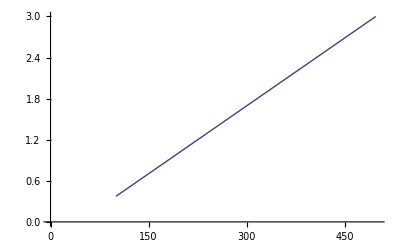

```mathematica
rho[t_] = (1/(59*10^6)) + 3.9*10^(-3)*(1/(59*10^6))*(t-300);
Plot[rho[t]*10^8, {t,100,500}, PlotRange->{{0,500},{0,3}}]
```

```mathematica
1.38*10^{-23}*300/(1.6*10^(-19))
```

{0.025875}

```mathematica
1/(Exp[ 5.5/0.052]+1)
```

1.16147×10^-46

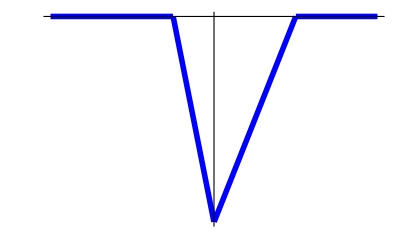

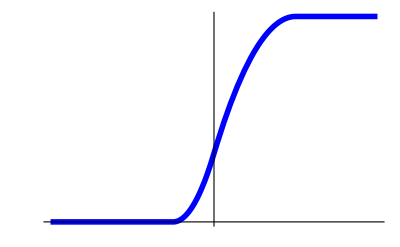

```mathematica
Efield[x_] = Piecewise[{{0,x<-0.5},{-2(x+0.5),-0.5<x<0}, {x-1, 0<x<1},{0,x>1}}];
pot[x_] = -1.0*Integrate[Efield[y], {y, -2,x}]; 

Plot[{Efield[x]},{x,-2,2}, Frame->False,FrameLabel->{"x", "E"},Ticks->False,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}]
Plot[{pot[x]},{x,-2,2}, Frame->False,FrameLabel->{"x", "E"},Ticks->False,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}]
```

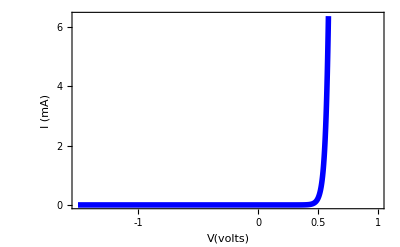

```mathematica
Clear[cur]; Clear[v];
cur[v_] = (1/10^9)(Exp[ (v)/0.026 ]-10 );
Plot[cur[x],{x,-1.5,1}, Frame->True,FrameLabel->{"V(volts)", "I (mA)"},FrameTicks->{{{-1,0, 2,4, 6, 8},None}, {{ -1, 0, 0.5,1},None}},
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}]
```

Integrate::pwrl: Unable to prove that integration limits {x} are real. Adding assumptions may help.

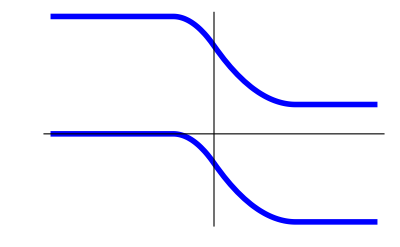

```mathematica
Efield[x_] = Piecewise[{{0,x<-0.5},{-2(x+0.5),-0.5<x<0}, {x-1, 0<x<1},{0,x>1}}];
pot[x_] = -1.0*Integrate[Efield[y], {y, -2,x}]; 
Plot[{-pot[x],1-pot[x]},{x,-2,2}, Frame->False,FrameLabel->{"x", "Energy"},Ticks->False,
 PlotStyle->{{Thickness->0.01, Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}]
```

Integrate::pwrl: Unable to prove that integration limits {x} are real. Adding assumptions may help.

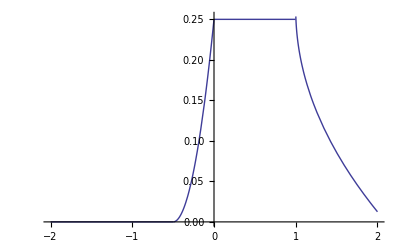

```mathematica
f[x_] = Piecewise[{{0,x<-0.5},{pot[x],-0.5<x<0},{pot[0],1>x>0},{1.05pot[0]-0.25Sqrt[(x-1)],x>1}}];
Plot[f[x],{x,-2,2}]
```

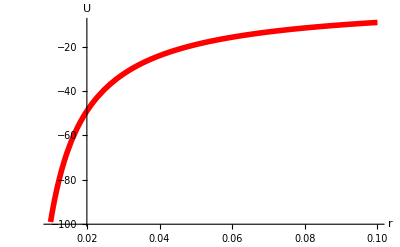

```mathematica
p1= Plot[  (-1/r)Exp[-r/1] ,{r, 0.01,0.1},AxesLabel->{"r", "U"},PlotRange->All,
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.01,Blue}}, TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
Show[p1]
```

```mathematica
Plot[{-1/r,+0.002/r^10,-1/r +0.002/r^10}, {r, 0.4,2.5}, PlotRange->{{0,2.5},{-3,3}}]
```

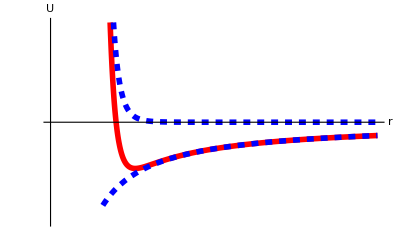

```mathematica
p1= Plot[  {-1/r +0.002/r^10,-1/r,+0.002/r^10}, {r, 0.4,2.5}, PlotRange->{{0,2.5},{-3,3}},AxesLabel->{"r", "U"},
 PlotStyle->{{Thickness->0.01, Red},{Dashed, Thickness->0.01,Blue},{Dashed, Thickness->0.01,Blue}}, Ticks->False,TextStyle->{FontColor->CMYKColor[0,0,0,1],FontFamily->"Frutiger-Roman",FontSize->24}];
Show[p1]
```